```mathematica
a=0.24
freq=
Y=200*^9
d=0.001
ν=0.303
ρ=7850
c=(1/(2*Pi))*Sqrt[(Y*d^2)/(12*ρ*(1-ν^2))]
k=Sqrt[freq/c]
nmax=50
```

0.24

120

200000000000

0.001

0.303

7850

0.243344

22.2065

50

```mathematica
kn[n1_,n2_]:=(Pi/a)*Sqrt[n1^2+n2^2]
```

```mathematica
mode[x_,y_,n1_,n2_]:=(2/a)*Cos[n1*Pi*x/a]*Cos[n2*Pi*y/a]
```

```mathematica
g[x_,y_,k_]:=Sum[mode[a/2,a/2,n1,n2]*mode[x,y,n1,n2]/(kn[n1,n2]^2-k^2), {n1,0,nmax},{n2,0,nmax}]
```

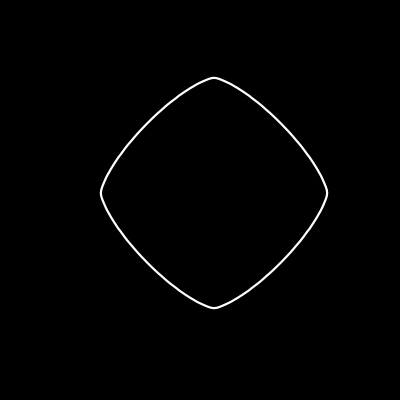

```mathematica
gc=ContourPlot[g[x,y,k]==0,{x,0,a},{y,0,a}, Background->Black, ContourStyle->White,PlotTheme->"Minimal"]
```

Now do upper and lower uncertainties

```mathematica
Y=200*^9
d=0.001+0.00005
ν=0.303
ρ=7850
c=(1/(2*Pi))*Sqrt[(Y*d^2)/(12*ρ*(1-ν^2))]
k=Sqrt[freq/c]
```

200000000000

0.00105

0.303

7850

0.255511

21.6713

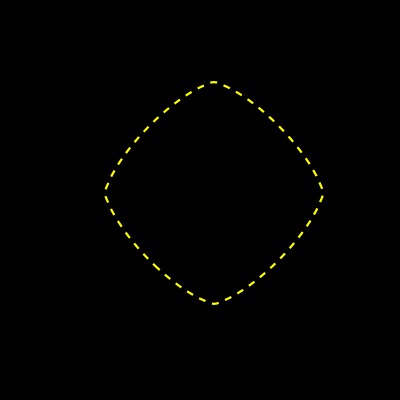

```mathematica
gcUpper=ContourPlot[g[x,y,k]==0,{x,0,a},{y,0,a}, Background->Black, ContourStyle->{Yellow,Dashed},PlotTheme->"Minimal"]
```

```mathematica
Y=200*^9
d=0.001-0.00005
ν=0.303
ρ=7850
c=(1/(2*Pi))*Sqrt[(Y*d^2)/(12*ρ*(1-ν^2))]
k=Sqrt[freq/c]
```

200000000000

0.00095

0.303

7850

0.231177

22.7834

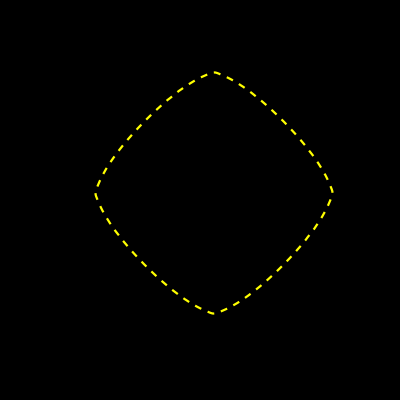

```mathematica
gcLower=ContourPlot[g[x,y,k]==0,{x,0,a},{y,0,a}, Background->Black, ContourStyle->{Yellow,Dashed},PlotTheme->"Minimal"]
```

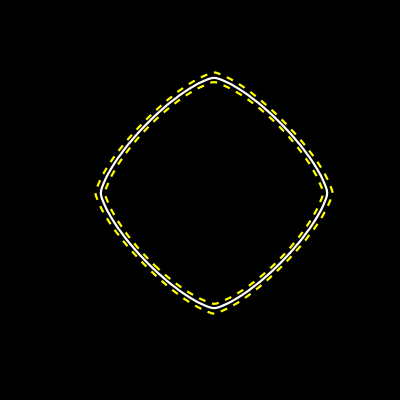

```mathematica
gcAll=Show[gc,gcUpper,gcLower]
```